```mathematica
P={{a,1-a},{1-b,b}}
```

{{a,1-a},{1-b,b}}

```mathematica
P//MatrixForm
```

(a | 1-a
1-b | b)

```mathematica
x=Eigensystem[Transpose[P]][[2]][[1]]
FullSimplify[x/Total[x]]
```

{-(1-b)/(-1+a),1}

{(-1+b)/(-2+a+b),(-1+a)/(-2+a+b)}

```mathematica
Solve[{(-1+b)/(-2+a+b)==π0,(-1+b)/(-2+a+b)(1-a)==k/L},{a,b}]
```

{{a→(-k+L π0)/(L π0),b→(k-L+L π0)/(L (-1+π0))}}

```mathematica
Mean[BetaDistribution[α1,β1]]
```

α1/(α1+β1)

```mathematica
Solve[{
(-1+Mean[BetaDistribution[α2,β2]])/(-2+Mean[BetaDistribution[α1,β1]]+Mean[BetaDistribution[α2,β2]])==π0,(-1+Mean[BetaDistribution[α2,β2]])/(-2+Mean[BetaDistribution[α1,β1]]+Mean[BetaDistribution[α2,β2]])(1-Mean[BetaDistribution[α1,β1]])==k/L,
 α1+β1==π0 L,
 α2+β2==(1-π0) L
},{α1,α2,β1,β2 }]
```

{{α1→-k+L π0,α2→-k+L-L π0,β1→k,β2→k}}

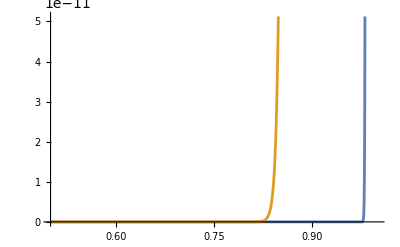

```mathematica
Plot[{PDF[BetaDistribution[-k+L π0,k]/.L->2000/.k->2/. π0->0.90,x],PDF[BetaDistribution[-k+L-L π0,k]/.L->2000/.k->2/. π0->0.90,x]},{x,0.5,1}]
```

```mathematica
Solve[{
α1/(α1+ β1)==(π0-k/L)/π0, (π0+k/L-1)/(π0-1)==α2/(α2+β2),
 α1+β1==π0 L,
 α2+β2==(1-π0) L
},{α1,α2,β1,β2 }]
```

{{α1→-k+L π0,α2→-k+L-L π0,β1→k,β2→k}}

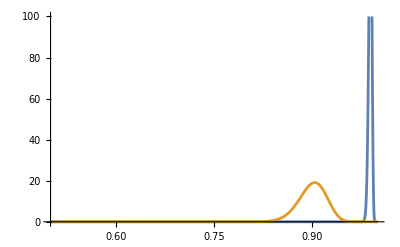

```mathematica
Plot[{PDF[BetaDistribution[-k+L π0,k]/.L->2000/.k->20/. π0->0.90,x],PDF[BetaDistribution[-k+L-L π0,k]/.L->2000/.k->20/. π0->0.90,x]},{x,0.5,1}, PlotRange->{-0.05,100}]
```

```mathematica
Manipulate[Plot[Exp[-lambda*d],{d,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->{"d","e^(-λd)"},PlotLabel->"Plot of Exp[-λd] for λ = "<>ToString[lambda]],{{lambda,1,"λ"},1,100,1,Appearance->"Labeled"}]
```